# Companion notebook for Postema et al. 2027

## Additional figure generation code for “Angular momenta and pressure relationships in rotating terrestrial planets”

Data to produce these figures is extracted from HERCULES runs and written to a file read by this notebook by either HERCULES_analysis.ipynb or Manuscript_figures.ipynb.

#### Generating cubic and quartic fits

This is an expanded version of what was done to produce the fits in Table 3. Data for each file is written to the root directory of this repository.

```mathematica
data=Import["[ROOT DIRECTORY]\\M1.9PyroSCmeltSMwarm_out.csv"];
```

```mathematica
(*data[[1]][[2]]
data[[-1]][[2]]
data[[-1]][[1]]*)
cubform[x_]=Fit[data,{1,x,x^2,x^3},x]
cubf=LinearModelFit[data,{1,x,x^2,x^3},x];
cubf[{"RSquared","ANOVATable","BestFitParameters"}]
```

207.124-0.772685 x-2.25904 x^2+0.114699 x^3

{0.999908, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 200748. | 200748. | 1.2976×10^6 | 1.04883×10^-245
x^2 | 1 | 1898.83 | 1898.83 | 12273.7 | 1.6959×10^-123
x^3 | 1 | 871.941 | 871.941 | 5636.08 | 2.40139×10^-103
Error | 121 | 18.7195 | 0.154707 |  | 
Total | 124 | 203537. |  |  | ,{207.124,-0.772685,-2.25904,0.114699}}

```mathematica
quartform[x_]=Fit[data,{1,x,x^2,x^3,x^4},x]
```

206.779+0.0940367 x-2.68499 x^2+0.181119 x^3-0.00319633 x^4

```mathematica
(*Show[Plot[{cubform[x]},{x,data[[1]][[1]],data[[-1]][[1]]},AxesLabel->{"Angular Momentum [L_EM]","CMB Pressure [GPa]"},ImageSize->Large],ListPlot[data,PlotStyle->Directive[PointSize->Medium],PlotLegends->{"HERCULES data"}]]*)
```

This is expanded code to find the fit forms of Equations 3 & 5

```mathematica
coeffdata=Import["[ROOT DIRECTORY]\\fitdeg3_k3.csv"];
```

```mathematica
FindFormula[coeffdata,z,4,All]
```

```mathematica
compLog[x_]=Fit[coeffdata,{1,ⅇ^-x,Log[x]},x]
simpleLog[x_]=Fit[coeffdata,{1,Log[x]},x]
otherLog[x_]=Fit[coeffdata,{1,x,Log[x]},x]
```

0.767648-1.50916 ⅇ^-x-4.23996 Log[x]

0.0176236-4.06686 Log[x]

-0.450129+0.577474 x-4.18019 Log[x]

```mathematica
lm=LinearModelFit[coeffdata,{1,x,Log[x]},x]
lm[{"RSquared","AdjustedRSquared","FitResiduals","ANOVATable"}]
lma=LinearModelFit[coeffdata,{1,ⅇ^-x,Log[x]},x]
lma[{"RSquared","AdjustedRSquared","FitResiduals","ANOVATable"}]
```

FittedModel[-0.450129+0.577474 x-4.18019 Log[x]]

{0.999913,0.999905,{0.125822,0.0564118,0.0540534,-0.036773,-0.0839509,-0.0959249,-0.1068,-0.056878,-0.0441647,-0.0709274,-0.0308379,0.0131105,-0.00862649,-0.0473759,-0.0325001,0.0249489,0.0743715,0.0809576,0.0731813,0.106045,0.0287791,0.0889652,0.0637571,-0.0115933,-0.164051}, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 861.385 | 861.385 | 140560. | 2.31872×10^-43
Log[x] | 1 | 689.068 | 689.068 | 112442. | 2.69995×10^-42
Error | 22 | 0.134821 | 0.00612823 |  | 
Total | 24 | 1550.59 |  |  | }

FittedModel[0.767648-1.50916 ⅇ^-x-4.23996 Log[x]]

{0.999985,0.999984,{0.0333056,0.00375719,0.0241002,-0.0298603,-0.0525835,-0.0380805,-0.039203,0.0121346,0.0261394,-0.00306023,0.0229787,0.0619354,0.0224801,-0.0283406,-0.0321498,-0.0141515,0.0297588,0.0257443,0.00791037,0.0256719,-0.0571855,-0.00147159,0.0234465,-0.00235033,-0.0209261}, | DF | SS | MS | F-Statistic | P-Value
ⅇ^-x | 1 | 1112.51 | 1112.51 | 1.08156×10^6 | 4.14767×10^-53
Log[x] | 1 | 438.051 | 438.051 | 425863. | 1.17555×10^-48
Error | 22 | 0.0226297 | 0.00102862 |  | 
Total | 24 | 1550.59 |  |  | }

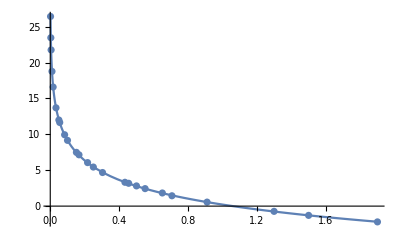

```mathematica
Show[Plot[compLog[x],{x,coeffdata[[1]][[1]],coeffdata[[-1]][[1]]},PlotRange->All],ListPlot[coeffdata]]
```

```mathematica
coeffdata2=Import["[ROOT DIRECTORY]\\fitdeg3_k2.csv"]
```

{{0.00166708,18.043},{0.00333284,16.2284},{0.00499998,15.1869},{0.0100073,13.3544},{0.0166803,12.0169},{0.0333223,10.2522},{0.0500252,9.21012},{0.0549996,9.02097},{0.0833684,7.97566},{0.100068,7.49137},{0.151772,6.49065},{0.166722,6.28648},{0.216638,5.62309},{0.250071,5.24566},{0.303408,4.79576},{0.433447,3.99838},{0.454995,3.91752},{0.500418,3.70111},{0.550419,3.47982},{0.650453,3.11797},{0.706197,2.88159},{0.910128,2.38106},{1.29894,1.6498},{1.49941,1.32138},{1.89899,0.792967}}

```mathematica
compLog2[x_]=Fit[coeffdata2,{1,ⅇ^-x,Log[x]},x]
simpleLog2[x_]=Fit[coeffdata2,{1,Log[x]},x]
otherLog2[x_]=Fit[coeffdata2,{1,x,Log[x]},x]
```

2.6539-1.26687 ⅇ^-x-2.6007 Log[x]

2.02429-2.45539 Log[x]

1.6275+0.489868 x-2.55152 Log[x]

```mathematica
lm2=LinearModelFit[coeffdata2,{1,x,Log[x]},x]
lm2[{"RSquared","AdjustedRSquared","FitResiduals","ANOVATable"}]
lm2a=LinearModelFit[coeffdata2,{1,ⅇ^-x,Log[x]},x]
lm2a[{"RSquared","AdjustedRSquared","FitResiduals","ANOVATable"}]
```

FittedModel[1.6275+0.489868 x-2.55152 Log[x]]

{0.999861,0.999848,{0.0933732,0.0455411,0.0381315,-0.0263753,-0.0635345,-0.0706903,-0.0842849,-0.033983,-0.0319011,-0.0585119,-0.0217708,0.00643436,-0.0131491,-0.0407772,-0.0235063,0.0255199,0.057894,0.0620239,0.0592453,0.0744619,0.0205766,0.0674477,0.0533419,-0.00707651,-0.12843}, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 308.756 | 308.756 | 86150.1 | 5.05199×10^-41
Log[x] | 1 | 256.726 | 256.726 | 71632.4 | 3.84443×10^-40
Error | 22 | 0.0788466 | 0.00358394 |  | 
Total | 24 | 565.561 |  |  | }

FittedModel[2.6539-1.26687 ⅇ^-x-2.6007 Log[x]]

{0.999977,0.999975,{0.0179905,0.00293527,0.0141849,-0.0200436,-0.0371516,-0.0226889,-0.0284185,0.0230024,0.0258968,-0.00285736,0.0219355,0.0459326,0.0114678,-0.0262667,-0.0246027,-0.00838734,0.0194207,0.0147884,0.00372652,0.00660846,-0.0517684,-0.00786513,0.0217354,0.00379432,-0.00336935}, | DF | SS | MS | F-Statistic | P-Value
ⅇ^-x | 1 | 400.739 | 400.739 | 687306. | 6.07643×10^-51
Log[x] | 1 | 164.809 | 164.809 | 282664. | 1.06688×10^-46
Error | 22 | 0.0128273 | 0.000583058 |  | 
Total | 24 | 565.561 |  |  | }

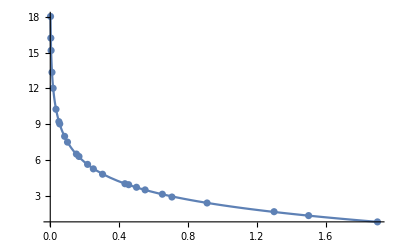

```mathematica
Show[Plot[compLog2[x],{x,coeffdata2[[1]][[1]],coeffdata2[[-1]][[1]]},PlotRange->All],ListPlot[coeffdata2]]
```

```mathematica
coeffdata3=Import["[ROOT DIRECTORY]\\fitdeg3_k1.csv"]
```

{{0.00166708,5.35578},{0.00333284,4.32737},{0.00499998,3.52394},{0.0100073,3.27211},{0.0166803,3.06968},{0.0333223,2.33464},{0.0500252,2.2912},{0.0549996,2.09646},{0.0833684,1.03216},{0.100068,1.67831},{0.151772,1.01452},{0.166722,0.819529},{0.216638,1.20343},{0.250071,1.38074},{0.303408,1.15853},{0.433447,0.591133},{0.454995,0.25611},{0.500418,0.245457},{0.550419,0.268727},{0.650453,0.246364},{0.706197,0.670486},{0.910128,0.201338},{1.29894,-0.367473},{1.49941,-0.153874},{1.89899,-0.0748729}}

```mathematica
compLog3[x_]=Fit[coeffdata3,{1,ⅇ^-x,Log[x]},x]
simpleLog3[x_]=Fit[coeffdata3,{1,Log[x]},x]
otherLog3[x_]=Fit[coeffdata3,{1,x,Log[x]},x]
```

0.486417-1.04161 ⅇ^-x-0.857402 Log[x]

-0.0312462-0.737928 Log[x]

-0.34801+0.391068 x-0.814676 Log[x]

```mathematica
lm3=LinearModelFit[coeffdata3,{1,x,Log[x]},x]
lm3[{"RSquared","AdjustedRSquared","FitResiduals","ANOVATable"}]
lm3a=LinearModelFit[coeffdata3,{1,ⅇ^-x,Log[x]},x]
lm3a[{"RSquared","AdjustedRSquared","FitResiduals","ANOVATable"}]
```

FittedModel[-0.34801+0.391068 x-0.814676 Log[x]]

{0.96154,0.958043,{0.491914,0.0272208,-0.446423,-0.134922,0.0762659,-0.101525,0.179505,0.0600504,-0.676481,0.111881,-0.232794,-0.357094,0.220653,0.50181,0.416238,0.0885794,-0.215346,-0.16624,-0.0849363,-0.0103776,0.458932,0.116708,-0.314359,-0.0622325,0.052973}, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 25.2469 | 25.2469 | 270.06 | 7.72307×10^-14
Log[x] | 1 | 26.1722 | 26.1722 | 279.958 | 5.34627×10^-14
Error | 22 | 2.0567 | 0.0934862 |  | 
Total | 24 | 53.4758 |  |  | }

FittedModel[0.486417-1.04161 ⅇ^-x-0.857402 Log[x]]

{0.96283,0.95945,{0.424707,-0.0114672,-0.468858,-0.130928,0.0978401,-0.0607822,0.227451,0.109076,-0.626165,0.160659,-0.193488,-0.321207,0.244322,0.517108,0.418525,0.0631865,-0.244634,-0.203045,-0.128918,-0.0652872,0.399866,0.0533993,-0.345464,-0.0604285,0.144532}, | DF | SS | MS | F-Statistic | P-Value
ⅇ^-x | 1 | 33.575 | 33.575 | 371.607 | 2.87195×10^-15
Log[x] | 1 | 17.9131 | 17.9131 | 198.262 | 1.7417×10^-12
Error | 22 | 1.98772 | 0.0903507 |  | 
Total | 24 | 53.4758 |  |  | }

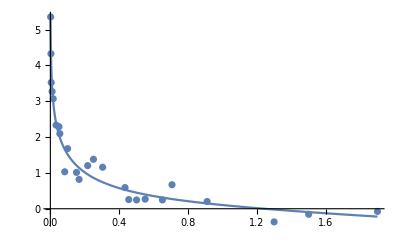

```mathematica
Show[Plot[compLog3[x],{x,0.001,coeffdata3[[-1]][[1]]},PlotRange->All],ListPlot[coeffdata3],PlotRange->All]
```

```mathematica
coeffdata4=Import["[ROOT DIRECTORY]\\fitdeg3_k0.csv"]
```

{{0.00166708,-0.274466},{0.00333284,0.196709},{0.00499998,0.475286},{0.0100073,0.957436},{0.0166803,1.31879},{0.0333223,1.81817},{0.0500252,2.12053},{0.0549996,2.22931},{0.0833684,2.50708},{0.100068,2.65136},{0.151772,2.98076},{0.166722,3.05786},{0.216638,3.27508},{0.250071,3.39585},{0.303408,3.56095},{0.433447,3.87299},{0.454995,3.91631},{0.500418,4.00269},{0.550419,4.09129},{0.650453,4.24802},{0.706197,4.32745},{0.910128,4.57754},{1.29894,4.93834},{1.49941,5.08677},{1.89899,5.33369}}

```mathematica
compLog4[x_]=Fit[coeffdata4,{1,ⅇ^-x,Log[x]},x]
simpleLog4[x_]=Fit[coeffdata4,{1,Log[x]},x]
otherLog4[x_]=Fit[coeffdata4,{1,x,Log[x]},x]
```

4.97856-0.799632 ⅇ^-x+0.698548 Log[x]

4.58116+0.790267 Log[x]

4.32583+0.315216 x+0.728405 Log[x]

```mathematica
lm4=LinearModelFit[coeffdata4,{1,x,Log[x]},x]
lm4[{"RSquared","AdjustedRSquared","FitResiduals","ANOVATable"}]
lm4a=LinearModelFit[coeffdata4,{1,ⅇ^-x,Log[x]},x]
lm4a[{"RSquared","AdjustedRSquared","FitResiduals","ANOVATable"}]
```

FittedModel[4.32583+0.315216 x+0.728405 Log[x]]

{0.999659,0.999628,{0.0585552,0.0246013,0.00720425,-0.0176493,-0.0305506,-0.0404687,-0.039326,-0.00116778,-0.0353134,-0.0292914,-0.0195978,-0.0156372,-0.00491958,0.000768711,0.0082348,0.0194607,0.0206584,0.0234056,0.0268717,0.0304343,0.0323981,0.0334172,0.0125505,-0.00676042,-0.0578785}, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 37.8497 | 37.8497 | 41502.7 | 1.55304×10^-37
Log[x] | 1 | 20.9227 | 20.9227 | 22941.9 | 1.04985×10^-34
Error | 22 | 0.0200636 | 0.000911983 |  | 
Total | 24 | 58.7925 |  |  | }

FittedModel[4.97856-0.799632 ⅇ^-x+0.698548 Log[x]]

{0.999938,0.999933,{0.0136652,-0.000408544,-0.00649723,-0.0130291,-0.0138377,-0.0108277,-0.00510007,0.0336824,-0.000270894,0.00428303,0.00625431,0.00753783,0.00885368,0.0081946,0.00590259,-0.00321994,-0.0048318,-0.00745431,-0.00902801,-0.0128461,-0.0134789,-0.0134053,-0.00476515,0.00377198,0.026855}, | DF | SS | MS | F-Statistic | P-Value
ⅇ^-x | 1 | 46.8985 | 46.8985 | 285164. | 9.68404×10^-47
Log[x] | 1 | 11.8903 | 11.8903 | 72298.5 | 3.4724×10^-40
Error | 22 | 0.00361816 | 0.000164462 |  | 
Total | 24 | 58.7925 |  |  | }

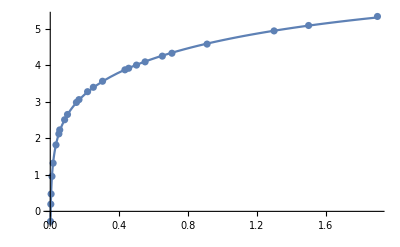

```mathematica
Show[Plot[compLog4[x],{x,coeffdata4[[1]][[1]],coeffdata4[[-1]][[1]]},PlotRange->All],ListPlot[coeffdata4]]
```

```mathematica
(* maxLdata=Import["C:\\Users\\gerri\\Postema_chapter3\\corol_L.csv"]*)
maxLdata=Import["[ROOT DIRECTORY]\\chosen_maxL.csv"]
```

{{0.00166708,0.00012447},{0.00333284,0.000395022},{0.00499998,0.000744423},{0.0100073,0.0024012},{0.0166803,0.00555131},{0.0333223,0.0171577},{0.0500252,0.0338137},{0.0549996,0.0383633},{0.0833684,0.0773206},{0.100068,0.105058},{0.151772,0.200731},{0.166722,0.239186},{0.216638,0.362585},{0.250071,0.459228},{0.303408,0.623892},{0.433447,1.10419},{0.454995,1.18863},{0.500418,1.38262},{0.550419,1.61359},{0.650453,2.09292},{0.706197,2.39475},{0.910128,3.55741},{1.29894,6.19806},{1.49941,7.7463},{1.89899,11.1233}}

```mathematica
FindFormula[maxLdata[[1;;-3]],z,4,All]
```

These are various attempts to find the form of the CoRoL scaling law:

```mathematica
FindFit[maxLdata[[1;;-3]],k1 x^k2+k3,{k1,k2,k3},x]
```

{k1→4.11985,k2→1.56839,k3→-0.00488567}

```mathematica
FindFit[maxLdata,k1 x^k2+k3,{k1,k2,k3},x]
```

{k1→4.11996,k2→1.55367,k3→-0.0100121}

```mathematica
FindFit[maxLdata[[1;;-3]],k1 x^k2,{k1,k2},x]
```

{k1→4.11381,k2→1.57216}

```mathematica
nlm=NonlinearModelFit[maxLdata,k1 x^k2+k3,{k1,k2,k3},x]
nlm[{"RSquared","FitResiduals","ANOVATable","BestFitParameters"}]
```

FittedModel[-0.0100121+4.11996 x^1.55367]

{0.999986,{0.00993766,0.00982348,0.00966044,0.00919188,0.00843835,0.00629053,0.00457333,0.00289408,0.0005386,-0.000191426,-0.00941736,-0.00556036,-0.0100932,-0.00904346,-0.0119527,-0.00991513,-0.0134918,-0.0126312,-0.0057565,-0.00906192,0.00496721,0.00823205,0.0226111,0.0256692,-0.0257128}, | DF | SS | MS
Model | 3 | 252.911 | 84.3038
Error | 22 | 0.00343849 | 0.000156295
Uncorrected Total | 25 | 252.915 | 
Corrected Total | 24 | 187.083 | ,{k1→4.11996,k2→1.55367,k3→-0.0100121}}

```mathematica
nlm2=NonlinearModelFit[maxLdata,k1 x^k2,{k1,k2},x,Method->NMinimize]
nlm2[{"RSquared","FitResiduals","ANOVATable","BestFitParameters"}]
```

FittedModel[4.10531 x^1.55849]

{0.999982,{-0.0000677502,-0.000170805,-0.000320252,-0.000738327,-0.0014097,-0.00330893,-0.00473845,-0.00632698,-0.00813511,-0.0085261,-0.0166616,-0.0124836,-0.015943,-0.014181,-0.0159786,-0.0114252,-0.0146177,-0.0129815,-0.00530922,-0.00720678,0.00749318,0.0124818,0.0268084,0.0280766,-0.0304963}, | DF | SS | MS
Model | 2 | 252.91 | 126.455
Error | 23 | 0.00460083 | 0.000200036
Uncorrected Total | 25 | 252.915 | 
Corrected Total | 24 | 187.083 | ,{k1→4.10531,k2→1.55849}}

```mathematica
(Map[nlm2,maxLdata[[All,1]]]-maxLdata[[All,2]])/Map[nlm2,maxLdata[[All,1]]]
```

{0.352461,0.301868,0.300798,0.235171,0.202513,0.161674,0.12291,0.141574,0.0951968,0.0750641,0.0766426,0.049603,0.0421185,0.0299551,0.0249716,0.0102412,0.0121486,0.00930172,0.00327952,0.00343159,-0.00313883,-0.00352102,-0.00434408,-0.0036377,0.00273418}

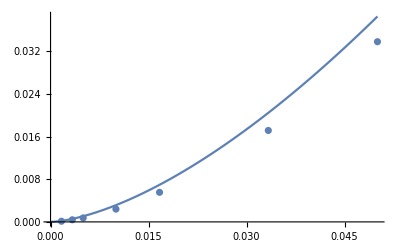

```mathematica
Show[Plot[nlm2[x],{x,0,maxLdata[[7]][[1]]},PlotRange->Full],ListPlot[maxLdata]]
```

```mathematica
logmaxLdata=Thread[{maxLdata[[All,1]],Log[maxLdata[[All,2]]]}]
```

{{0.00166708,-8.99144},{0.00333284,-7.83657},{0.00499998,-7.2029},{0.0100073,-6.03179},{0.0166803,-5.19372},{0.0333223,-4.06531},{0.0500252,-3.38689},{0.0549996,-3.26065},{0.0833684,-2.5598},{0.100068,-2.25324},{0.151772,-1.60579},{0.166722,-1.43051},{0.216638,-1.0145},{0.250071,-0.778208},{0.303408,-0.471778},{0.433447,0.0991154},{0.454995,0.172798},{0.500418,0.323978},{0.550419,0.478463},{0.650453,0.738561},{0.706197,0.873278},{0.910128,1.26903},{1.29894,1.82424},{1.49941,2.04722},{1.89899,2.40904}}

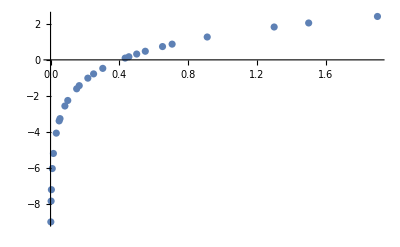

```mathematica
ListPlot[logmaxLdata]
```

```mathematica
FindFormula[logmaxLdata,z,4,All]
```

```mathematica
nlm3=LinearModelFit[logmaxLdata,{1,x,Log[x]},x]
nlm3[{"RSquared","FitResiduals","ANOVATable","BestFitParameters"}]
nlm4=LinearModelFit[logmaxLdata,{1,ⅇ^-x,Log[x]},x]
nlm4[{"RSquared","FitResiduals","ANOVATable","BestFitParameters"}]
```

FittedModel[1.51209-0.0883216 x+1.64019 Log[x]]

{0.999989,{-0.0115889,0.0071852,-0.0242775,0.00918317,0.00984104,0.00471148,0.0181919,-0.0106233,0.010514,0.0190781,-0.0120968,0.0104112,0.0012651,0.00510996,-0.000851518,-0.00351549,-0.00750543,-0.00839086,-0.00569575,-0.0106572,-0.00588074,-0.00821647,-0.00212058,0.00315503,0.0127744}, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 140.684 | 140.684 | 1.12751×10^6 | 2.62437×10^-53
Log[x] | 1 | 106.087 | 106.087 | 850230. | 5.85366×10^-52
Error | 22 | 0.00274503 | 0.000124774 |  | 
Total | 24 | 246.774 |  |  | ,{1.51209,-0.0883216,1.64019}}

FittedModel[1.33045+0.221544 ⅇ^-x+1.64827 Log[x]]

{0.999992,{0.000406252,0.0138052,-0.0207136,0.00780063,0.00520065,-0.00339291,0.00887958,-0.0200952,0.00104156,0.0100313,-0.0189743,0.00427876,-0.00226103,0.0033372,0.0000640647,0.00297843,-0.000244982,0.000330843,0.00439131,0.00140819,0.00686495,0.00463879,0.00224422,-0.000366038,-0.0116539}, | DF | SS | MS | F-Statistic | P-Value
ⅇ^-x | 1 | 180.571 | 180.571 | 2.04972×10^6 | 3.66234×10^-56
Log[x] | 1 | 66.2002 | 66.2002 | 751457. | 2.277×10^-51
Error | 22 | 0.00193811 | 0.0000880957 |  | 
Total | 24 | 246.774 |  |  | ,{1.33045,0.221544,1.64827}}

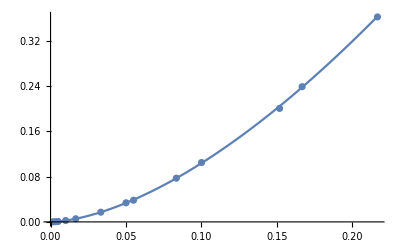

```mathematica
Show[Plot[ⅇ^nlm4[x],{x,0,logmaxLdata[[13]][[1]]}],ListPlot[maxLdata]]
```

```mathematica
nlm5=NonlinearModelFit[maxLdata,k3 x^k2 ⅇ^(k1 x),{k1,k2,k3},x,Method->NMinimize]
nlm5[{"RSquared","FitResiduals","ANOVATable","BestFitParameters"}]
nlm6=NonlinearModelFit[maxLdata,k3 x^k2 ⅇ^(k1 ⅇ^-x),{k1,k2,k3},x,Method->NMinimize,MaxIterations->10000]
nlm6[{"RSquared","FitResiduals","ANOVATable","BestFitParameters"}]
```

FittedModel[4.31904 ⅇ^(-0.0457691 x) x^1.61064]

{0.999999,{-0.0000203833,-0.0000470268,-0.000105065,-0.000195491,-0.000359774,-0.000846914,-0.000800674,-0.00195193,-0.00135752,-0.00043743,-0.0051267,-0.000136631,-0.00148989,0.00117559,0.0000287404,0.00263659,-0.00128715,-0.00150539,0.00369725,-0.00416668,0.00680519,-0.00238385,-0.00375496,0.00295257,-0.000223897}, | DF | SS | MS
Model | 3 | 252.915 | 84.3049
Error | 22 | 0.000154055 | 7.00248×10^-6
Uncorrected Total | 25 | 252.915 | 
Corrected Total | 24 | 187.083 | ,{k1→-0.0457691,k2→1.61064,k3→4.31904}}

FittedModel[4.03096 ⅇ^(0.0501374 ⅇ^-x) x^1.57541]

{0.999982,{-0.0000535949,-0.000135275,-0.000260189,-0.00059546,-0.00114842,-0.00275661,-0.0039266,-0.00544576,-0.00693,-0.00718514,-0.015121,-0.0109378,-0.0145095,-0.012908,-0.0150526,-0.0115094,-0.0148629,-0.0135424,-0.00616956,-0.0084783,0.00611171,0.0113907,0.0278686,0.0298306,-0.0314362}, | DF | SS | MS
Model | 3 | 252.91 | 84.3034
Error | 22 | 0.00457467 | 0.00020794
Uncorrected Total | 25 | 252.915 | 
Corrected Total | 24 | 187.083 | ,{k1→0.0501374,k2→1.57541,k3→4.03096}}

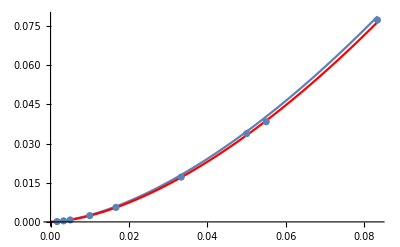

```mathematica
j=9;
Show[Plot[nlm5[x],{x,0,maxLdata[[j]][[1]]},PlotRange->Full],Plot[ⅇ^nlm3[x],{x,0,maxLdata[[j]][[1]]},PlotRange->Full,PlotStyle->Red],ListPlot[maxLdata]]
```

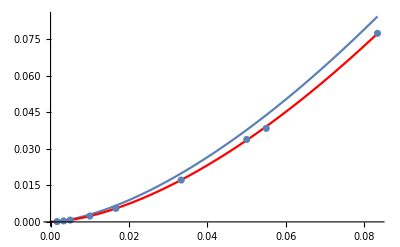

```mathematica
Show[Plot[nlm6[x],{x,0,maxLdata[[j]][[1]]},PlotRange->Full],Plot[ⅇ^nlm4[x],{x,0,maxLdata[[j]][[1]]},PlotRange->Full,PlotStyle->Red],ListPlot[maxLdata]]
```

5

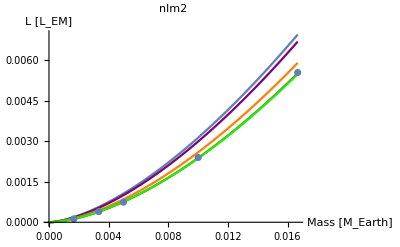

```mathematica
j=5
Show[Plot[nlm2[x],{x,0,maxLdata[[j]][[1]]},PlotRange->Full,AxesLabel->{Style["Mass [M_Earth]",Medium,Black],Style["L [L_EM]",Medium,Black]},PlotLabel->"nlm2"],Plot[nlm6[x],{x,0,maxLdata[[j]][[1]]},PlotRange->Full,PlotStyle->Purple,PlotLabel->"nlm6"],Plot[nlm5[x],{x,0,maxLdata[[j]][[1]]},PlotRange->Full,PlotStyle->Orange,PlotLabel->"nlm5"],Plot[ⅇ^nlm4[x],{x,0,maxLdata[[j]][[1]]},PlotRange->Full,PlotStyle->Red,PlotLabel->"nlm4"],Plot[ⅇ^nlm3[x],{x,0,maxLdata[[j]][[1]]},PlotRange->Full,PlotStyle->Green,PlotLabel->"nlm3"],ListPlot[maxLdata]]
```

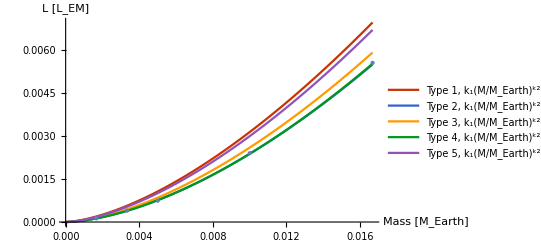

```mathematica
Show[Plot[{nlm2[x],ⅇ^nlm3[x],nlm5[x],ⅇ^nlm4[x],nlm6[x]},{x,0,maxLdata[[j]][[1]]},AxesLabel->{Style["Mass [M_Earth]",Medium,Black],Style["L [L_EM]",Medium,Black]},PlotLegends->{"Type 1, k_1(M/M_Earth)^k2","Type 2, k_1(M/M_Earth)^k2e^k_3, Log","Type 3, k_1(M/M_Earth)^k2e^k_3, Non-log","Type 4, k_1(M/M_Earth)^k2e^k_3, Log","Type 5, k_1(M/M_Earth)^k2e^k_3, Non-log"},PlotTheme->"VibrantColor"],ListPlot[maxLdata,PlotStyle->Directive[PointSize->Large]]]
```

```mathematica
Export["[ROOT DIRECTORY]",%%,"PDF"]
```

C:\Users\gerri\Postema_chapter3\herc_corol1_new.pdf

```mathematica
Export["[ROOT DIRECTORY]\\herc_corol1.pdf",%79,"PDF"]
```

C:\Users\gerri\Postema_chapter3\herc_corol1.pdf

## Figure 6:

We chose to use the fourth of our preliminary models to parameterize the CoRoL, as it had low errors and fit both high and low magnitudes well.

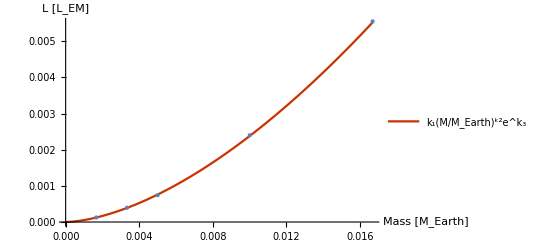

```mathematica
Show[Plot[{ⅇ^nlm4[x]},{x,0,maxLdata[[j]][[1]]},AxesLabel->{Style["Mass [M_Earth]",Medium,Black],Style["L [L_EM]",Medium,Black]},PlotLegends->{"k_1(M/M_Earth)^k2e^k_3"},PlotTheme->"VibrantColor"],ListPlot[maxLdata,PlotStyle->Directive[PointSize->Large]]]
```

```mathematica
Export["[ROOT DIRECTORY]\\herc_corol_single_a.pdf",%39,"PDF"]
```

C:\Users\gerri\Postema_chapter3\herc_corol_single_a.pdf

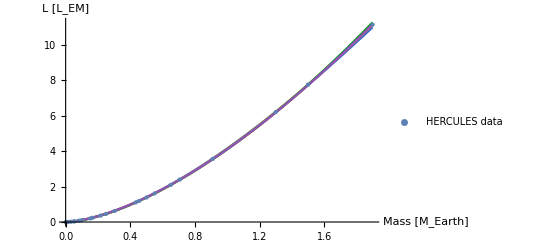

```mathematica
Show[Plot[{nlm2[x],ⅇ^nlm3[x],nlm5[x],ⅇ^nlm4[x],nlm6[x]},{x,0,maxLdata[[-1]][[1]]},AxesLabel->{Style["Mass [M_Earth]",Medium,Black],Style["L [L_EM]",Medium,Black]},PlotTheme->"VibrantColor"],ListPlot[maxLdata,PlotStyle->Directive[PointSize->Large],PlotLegends->{"HERCULES data"}]]
```

```mathematica
Export["[ROOT DIRECTORY]\\herc_corol2_new.pdf",%%,"PDF"]
```

C:\Users\gerri\Postema_chapter3\herc_corol2_new.pdf

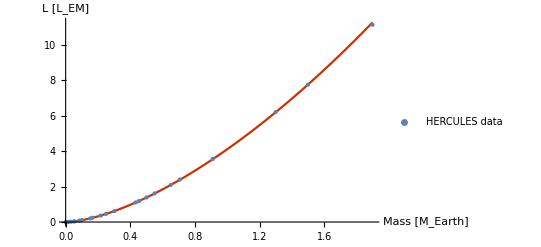

```mathematica
Show[Plot[{ⅇ^nlm4[x]},{x,0,maxLdata[[-1]][[1]]},AxesLabel->{Style["Mass [M_Earth]",Medium,Black],Style["L [L_EM]",Medium,Black]},PlotTheme->"VibrantColor"],ListPlot[maxLdata,PlotStyle->Directive[PointSize->Large],PlotLegends->{"HERCULES data"}]]
```

```mathematica
Export["[ROOT DIRECTORY]\\herc_corol_single_b.pdf",%%,"PDF"]
```

C:\Users\gerri\Postema_chapter3\herc_corol_single_b.pdf

```mathematica
resid2=(Map[nlm2,maxLdata[[All,1]]]-maxLdata[[All,2]])/Map[nlm2,maxLdata[[All,1]]];
resid3=(Map[Function[x,ⅇ^nlm3[x]],maxLdata[[All,1]]]-maxLdata[[All,2]])/Map[Function[x,ⅇ^nlm3[x]],maxLdata[[All,1]]];
resid5=(Map[nlm5,maxLdata[[All,1]]]-maxLdata[[All,2]])/Map[nlm5,maxLdata[[All,1]]];
resid4=(Map[Function[x,ⅇ^nlm4[x]],maxLdata[[All,1]]]-maxLdata[[All,2]])/Map[Function[x,ⅇ^nlm4[x]],maxLdata[[All,1]]];
resid6=(Map[nlm6,maxLdata[[All,1]]]-maxLdata[[All,2]])/Map[nlm6,maxLdata[[All,1]]];
```

Here are scaled residuals for all of our preliminary models. Type 4 is the version that is described in Table 2.

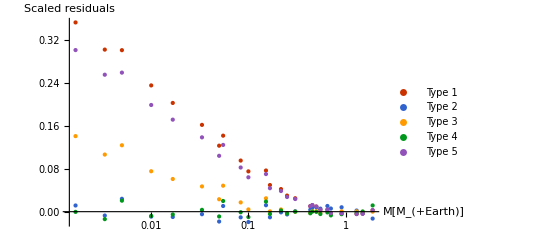

```mathematica
ListPlot[{Thread[{maxLdata[[All,1]],resid2}],Thread[{maxLdata[[All,1]],resid3}],Thread[{maxLdata[[All,1]],resid5}],Thread[{maxLdata[[All,1]],resid4}],Thread[{maxLdata[[All,1]],resid6}]},ScalingFunctions->{"Log",None},PlotStyle->Directive[PointSize->Large],AxesLabel->{Style["M[M_(+Earth)]",Medium,Black],Style["Scaled \n residuals",Medium,Black]},PlotRange->Full,PlotLegends->{"Type 1","Type 2","Type 3","Type 4","Type 5"},PlotTheme->"VibrantColor"]
```

```mathematica
Export["[ROOT DIRECTORY]\\corol_resid1.pdf",%%,"PDF"]
```

C:\Users\gerri\Postema_chapter3\corol_resid1.pdf

Here are scaled residuals for just the fourth model:

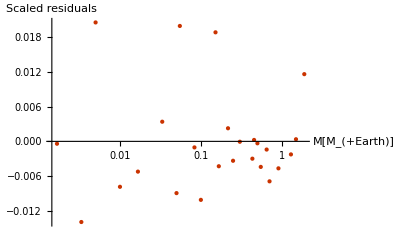

```mathematica
ListPlot[{Thread[{maxLdata[[All,1]],resid4}]},ScalingFunctions->{"Log",None},PlotStyle->Directive[PointSize->Large],AxesLabel->{Style["M[M_(+Earth)]",Medium,Black],Style["Scaled \n residuals",Medium,Black]},PlotRange->Full,PlotTheme->"VibrantColor"]
```

```mathematica
Export["[ROOT DIRECTORY]\\herc_corol_single_c.pdf",%%,"PDF"]
```

C:\Users\gerri\Postema_chapter3\herc_corol_single_c.pdf

Here are absolute residuals for all models:

```mathematica
aresid2=(Map[nlm2,maxLdata[[All,1]]]-maxLdata[[All,2]]);
aresid3=(Map[Function[x,ⅇ^nlm3[x]],maxLdata[[All,1]]]-maxLdata[[All,2]]);
aresid5=(Map[nlm5,maxLdata[[All,1]]]-maxLdata[[All,2]]);
aresid4=(Map[Function[x,ⅇ^nlm4[x]],maxLdata[[All,1]]]-maxLdata[[All,2]]);
aresid6=(Map[nlm6,maxLdata[[All,1]]]-maxLdata[[All,2]]);
```

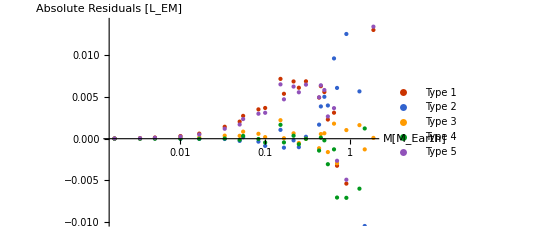

```mathematica
ListPlot[{Thread[{maxLdata[[All,1]],aresid2}],Thread[{maxLdata[[All,1]],aresid3}],Thread[{maxLdata[[All,1]],aresid5}],Thread[{maxLdata[[All,1]],aresid4}],Thread[{maxLdata[[All,1]],aresid6}]},ScalingFunctions->{"Log","SignedLog"},PlotStyle->Directive[PointSize->Large],AxesLabel->{Style["M[M_Earth]",Medium,Black],Style["Absolute \n Residuals [L_EM]",Medium,Black]},PlotRange->Automatic, PlotLegends->{"Type 1","Type 2","Type 3","Type 4","Type 5"},PlotTheme->"VibrantColor"]
```

```mathematica
Export["[ROOT DIRECTORY]\\corol_resid2.pdf",%%,"PDF"]
```

C:\Users\gerri\Postema_chapter3\corol_resid2.pdf

And here are absolute residuals for just the chosen model:

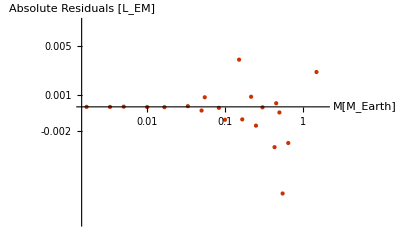

```mathematica
ListPlot[{Thread[{maxLdata[[All,1]],aresid4}]},ScalingFunctions->{"Log","SignedLog"},PlotStyle->Directive[PointSize->Large],AxesLabel->{Style["M[M_Earth]",Medium,Black],Style["Absolute \n Residuals [L_EM]",Medium,Black]},PlotRange->Automatic,PlotTheme->"VibrantColor"]
```

```mathematica
Export["[ROOT DIRECTORY]\\herc_corol_single_d.pdf",%%,"PDF"]
```

C:\Users\gerri\Postema_chapter3\herc_corol_single_d.pdf

```mathematica
bigData=Import["[ROOT DIRECTORY]\\alldataML.csv"]
```

{{0.00166708,0.,0.75892},{0.00166708,0.,0.758921},{0.00166708,2.85728×10^-7,0.758798},{0.00166708,5.71456×10^-7,0.758681},4751,{1.89899,10.467,82.9008},{1.89899,10.6573,80.7829},{1.89899,10.8476,78.7314},{1.89899,11.0379,76.8492}}
 |  |  |  |

```mathematica
bigfit=NonlinearModelFit[bigData,c00 M^c01 ⅇ^(c02 M)+c10 M^c11 ⅇ^(c12 M)L+c20 M^c21 ⅇ^(c22 M)L^2+c30 M^c31 ⅇ^(c32 M)L^3,{c00,c01,c02,c10,c11,c12,c20,c21,c22,c30,c31,c32},{M,L},Method->NMinimize]
bigfit[{"RSquared","AdjustedRSquared","ANOVATable","BestFitParameters"}]
```

FittedModel[(1.14606 ⅇ^(0.155901 M) L^3)/M^3.94774-(«18» ⅇ^(«1») L^2)/M^(«19»)+«1»-1.05085 ⅇ^(-«19» M) L M^75.6998]

{0.99992,0.99992, | DF | SS | MS
Model | 12 | 1.54792×10^7 | 1.28994×10^6
Error | 4747 | 1232.03 | 0.259539
Uncorrected Total | 4759 | 1.54805×10^7 | 
Corrected Total | 4758 | 9.80459×10^6 | ,{c00→90.1069,c01→0.823096,c02→0.163356,c10→-1.05085,c11→75.6998,c12→-26.0626,c20→-8.29442,c21→-2.34231,c22→0.136888,c30→1.14606,c31→-3.94774,c32→0.155901}}

```mathematica
bigfit2=NonlinearModelFit[bigData,c00 M^c01 ⅇ^(c02 ⅇ^-M)+c10 M^c11 ⅇ^(c12 ⅇ^-M)L+c20 M^c21 ⅇ^(c22 ⅇ^-M)L^2+c30 M^c31 ⅇ^(c32 ⅇ^-M)L^3,{c00,c01,c02,c10,c11,c12,c20,c21,c22,c30,c31,c32},{M,L},MaxIterations->10000]
bigfit2[{"RSquared","AdjustedRSquared","ANOVATable","BestFitParameters"}]
```

FittedModel[(2.78016 ⅇ^(-1.87479 «1») L^3)/M^4.26785+(«19» «1»«1»L)/M^(«18»)-«1»+153.54 ⅇ^(-0.959219«1»«1») M^0.663316]

{0.999905,0.999905, | DF | SS | MS
Model | 12 | 1.5479×10^7 | 1.28992×10^6
Error | 4747 | 1463.62 | 0.308325
Uncorrected Total | 4759 | 1.54805×10^7 | 
Corrected Total | 4758 | 9.80459×10^6 | ,{c00→153.54,c01→0.663316,c02→-0.959219,c10→243.19,c11→-3.36676,c12→-22.0412,c20→-18.3325,c21→-2.6533,c22→-1.67831,c30→2.78016,c31→-4.26785,c32→-1.87479}}

```mathematica
{0.9999054539031753,0.9999052148989281,{{"", "DF", "SS", "MS"}, {"Model", 12, 1.5479015079605293*^7, 1.289917923300441*^6}, {"Error", 4747, 1463.6188379149446, 0.3083250132536222}, {"Uncorrected Total", 4759, 1.5480478698443208*^7, }, {"Corrected Total", 4758, 9.804585477368403*^6, }},{c00->153.53959723963789,c01->0.6633160603278092,c02->-0.9592188598031302,c10->243.19051119279166,c11->-3.366759602220585,c12->-22.041247448477787,c20->-18.332505614890877,c21->-2.6533013645110426,c22->-1.6783109326520955,c30->2.780157903976064,c31->-4.267852305563586,c32->-1.874789905348047}}
```

{0.999905,0.999905, | DF | SS | MS
Model | 12 | 1.5479×10^7 | 1.28992×10^6
Error | 4747 | 1463.62 | 0.308325
Uncorrected Total | 4759 | 1.54805×10^7 | 
Corrected Total | 4758 | 9.80459×10^6 | ,{c00→153.54,c01→0.663316,c02→-0.959219,c10→243.191,c11→-3.36676,c12→-22.0412,c20→-18.3325,c21→-2.6533,c22→-1.67831,c30→2.78016,c31→-4.26785,c32→-1.87479}}

## Appendix Figure 12

```mathematica
Show[Plot3D[bigfit2[m,l],{m,0.001,2},{l,0,15},RegionFunction->Function[{m,l},0<l<ⅇ^(nlm4[m])],ImageSize->Full,PlotPoints->500,AxesLabel->{Style["Mass/M_Earth",Large,Bold],Style["L/L_EM",Large,Bold],Style["P_CMB(GPa)",Large,Bold]},Mesh->Automatic,PlotRange->{0,250},TicksStyle->Directive[FontSize->22]],ListPointPlot3D[bigData]]
```

-Graphics3D-

```mathematica
abigresid=bigfit2[{"FitResiduals"}];
bigresid=abigresid/{bigData[[All,3]]};
(*abigResid=Table[{bigData[[i,1]],bigData[[i,2]],abigresid[[1,i]]},{i,1,Length[bigData]}]*)
abigResid=Table[{bigData[[i,1]],bigData[[i,2]]/ⅇ^(nlm4[bigData[[i,1]]]),abigresid[[1,i]]},{i,1,Length[bigData]}]
(*bigResid=Table[{bigData[[i,1]],bigData[[i,2]],bigresid[[1,i]]},{i,1,Length[bigData]}]*)
bigResid=Table[{bigData[[i,1]],bigData[[i,2]]/ⅇ^(nlm4[bigData[[i,1]]]),bigresid[[1,i]]},{i,1,Length[bigData]}]
```

{{0.00166708,0.,-0.0875459},{0.00166708,0.,-0.0875452},{0.00166708,0.00229649,-0.0877055},{0.00166708,0.00459297,-0.0878457},{0.00166708,0.00688946,-0.0879502},4750,{1.89899,0.930097,-2.45798},{1.89899,0.947007,-2.97874},{1.89899,0.963918,-3.55964},{1.89899,0.980829,-4.10332}}
 |  |  |  |

{{0.00166708,0.,-0.115356},{0.00166708,0.,-0.115355},{0.00166708,0.00229649,-0.115585},{0.00166708,0.00459297,-0.115787},{0.00166708,0.00688946,-0.11594},4750,{1.89899,0.930097,-0.0296497},{1.89899,0.947007,-0.0368734},{1.89899,0.963918,-0.0452125},{1.89899,0.980829,-0.0533945}}
 |  |  |  |

```mathematica
bigResid[[1,3]]
```

-0.115355

```mathematica
ListPlot[Table[Style[{abigResid[[i,2]],abigResid[[i,3]]},ColorData["TemperatureMap"][abigResid[[i,1]]]],{i,1,Length[abigResid]}],ImageSize->Large,PlotRange->All,PlotLegends->Placed[BarLegend[{"TemperatureMap",{0,2}},LegendLabel->"Mass/M_Earth"],Right],AxesLabel->{Style["L/L_CoRoL",Medium,Bold],Style["Residual\nP_CMB(GPa)",Medium,Bold]},TicksStyle->Directive[FontSize->14]]
```

-Graphics-

```mathematica
Export["[ROOT DIRECTORY]\\aresid_2d.pdf",%%,"PDF"]
```

C:\Users\gerri\Postema_chapter3\aresid_2d.pdf

```mathematica
ListPlot[Table[Style[{bigResid[[i,2]],bigResid[[i,3]]},ColorData["TemperatureMap"][bigResid[[i,1]]]],{i,1,Length[bigResid]}],ImageSize->Large,PlotRange->All,PlotLegends->Placed[BarLegend[{"TemperatureMap",{0,2}},LegendLabel->"Mass/M_Earth"],Right],AxesLabel->{Style["L/L_CoRoL",Medium,Bold],Style["Scaled \nResdiual \nP_CMB",Medium,Bold]},TicksStyle->Directive[FontSize->14]]
```

-Graphics-

```mathematica
Export["[ROOT DIRECTORY]\\scaled_resid_2d.pdf",%%,"PDF"]
```

C:\Users\gerri\Postema_chapter3\scaled_resid_2d.pdf

```mathematica
ListPointPlot3D[abigResid,ImageSize->Full,AxesLabel->{Style["Mass/M_Earth",Large,Bold],Style["L/L_EM",Large,Bold],Style["Residual\nP_CMB(GPa)",Large,Bold]},PlotRange->All,TicksStyle->Directive[FontSize->22]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[bigResid,ImageSize->Full,AxesLabel->{Style["Mass/M_Earth",Large,Bold],Style["L/L_EM",Large,Bold],Style["Scaled \nResdiual \nP_CMB(GPa)",Large,Bold]},PlotRange->All,TicksStyle->Directive[FontSize->22]]
```

-Graphics3D-

```mathematica
Dimensions[bigresid]
```

{1,4759}

```mathematica
{bigData[[All,3]]};
```

```mathematica
Dimensions[%542]
```

{1,4759}

```mathematica
(*logBigData=Import["C:\\Users\\gerri\\Postema_chapter3\\LogalldataML.csv"]*)
```

```mathematica
(*bigfit3=NonlinearModelFit[bigData,c00 M^c01 ⅇ^(c02 ⅇ^-M)+c10 M^c11 ⅇ^(c12 ⅇ^-M)L+c20 M^c21 ⅇ^(c22 ⅇ^-M)L^2+c30 M^c31 ⅇ^(c32 ⅇ^-M)L^3+c40 M^c41 ⅇ^(c42 ⅇ^-M)L^4,{c00,c01,c02,c10,c11,c12,c20,c21,c22,c30,c31,c32,c40,c41,c42},{M,L},MaxIterations->1000000]
bigfit3[{"RSquared","AdjustedRSquared","ANOVATable","BestFitParameters"}]*)
```

```mathematica
(*Show[Plot3D[bigfit3[m,l],{m,0.001,2},{l,0,12},RegionFunction->Function[{m,l},0<l<nlm6[m]],ImageSize->Full,PlotPoints->100,AxesLabel->{"Mass/M_Earth","L/L_EM","P_CMB(GPa)"},Mesh->Automatic],ListPointPlot3D[bigData]]*)
```